1. Задаем начальные данные :

```mathematica
X={0,π/4,π/2}; f[x_]:=Cos[x]^3; F=f /@ X
```

{1,1/(2 √2),0}

```mathematica
n=Length[X]-1; m=2;
```

```mathematica
Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=F[[i+1]]},{i,0,n}]
Nn=(m+1)(n+1)-1;
```

```mathematica
Unprotect[Power]; 0^0=1;
```

2. Строим алгебраический интерполяционный многочлен:

```mathematica
H[x_]=∑_(k=0)^Nn Subscript[a, k] x^k;
```

```mathematica
eqv=Table[(D[H[x],{x,s}]//.x->Subscript[x, j])==(D[f[x],{x,s}]//.x->Subscript[x, j]),{s,0,m},{j,0,n}]//Flatten;
```

```mathematica
koef=Solve[eqv,{}]//Flatten;
```

```mathematica
H[x_]=∑_(k=0)^Nn Subscript[a, k] x^k//.koef//Expand;
```

3. Строим интерполяционный многочлен с помощью встроенной функции InterpolatingPolynomial:

```mathematica
Tb1=Table[{Subscript[x, j],Table[D[f[x],{x,s}]//.x->Subscript[x, j],{s,0,m}]},{j,0,n}]
```

{{0,{1,0,-3}},{π/4,{1/(2 √2),-3/(2 √2),3/(2 √2)}},{π/2,{0,0,0}}}

```mathematica
P1[x_]=InterpolatingPolynomial[Tb1,x]//Expand;
```

4. Сравниваем интерполяционные многочлены:

```mathematica
H[x]===P1[x]
```

True

5. Получаем оценку погрешности:

```mathematica
a=Subscript[x, 0];b=Subscript[x, n];
```

```mathematica
M=Maximize[{Abs[D[f[x],{x,Nn+1}]],a≤x≤b},x][[1]]//N
```

4921.13

```mathematica
Ω[y_]=∏_(j=0)^n (y-Subscript[x, j])^(m+1);
```

```mathematica
R=M/((Nn+1)!)*Maximize[{Abs[Ω[x]],a≤x≤b},x][[1]]
```

0.0000879336

6. Построить график абсолютной погрешности:

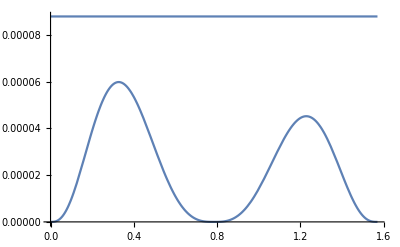

```mathematica
Gr1=Plot[Abs[f[x]-H[x]],{x,Subscript[x, 0],Subscript[x, n]}];
Gr2=Plot[R,{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2,PlotRange->{{Subscript[x, 0],Subscript[x, n]},{0,R}}]
```